## Variational Quantum Eigensolver

### Gabriel Oliveira Alves

Here I define a few symbolic operations:

```mathematica
(*Aesthetic Way to write tensor products. The function MatrixQ decides wether we should use the function for matrices, kron[], or for vectors, vkron[]*)
a_⊗b_:=If[MatrixQ[a]==True,kron[a,b],kronV[a,b]]

(*This makes an arbitrary number of products define, such as 0 ⊗ 0 ⊗ 0 ⊗ 1, etc...*)
a_⊗b_⊗c__:=(a⊗b)⊗c
```

Here we define the Hamiltonian from the problem statement

```mathematica
H:=({{1, 0, 0, 0}, {0, 0, -1, 0}, {0, -1, 0, 0}, {0, 0, 0, 1}})
```

```mathematica
H
```

{{1,0,0,0},{0,0,-1,0},{0,-1,0,0},{0,0,0,1}}

And we also define the Pauli Matrices:

```mathematica
σ0:=({{1, 0}, {0, 1}});
σx:=({{0, 1}, {1, 0}});
σy:=({{0, -ⅈ}, {ⅈ, 0}});
σz:=({{1, 0}, {0, -1}});
```

Below we try to decompose the matrix H using the form given in the hints:

H = α + β σ_z ⊗ σ_z +   γ  σ_x⊗ σ_x+ δ σ_y ⊗ σ_y

```mathematica
ClearAll[α,β,γ,δ];
Solution = Solve[H==α σ0 ⊗ σ0 + β σz ⊗ σz + γ σx ⊗ σx + δ σy ⊗ σy,{α,β,γ,δ}]
```

{{α→1/2,β→1/2,γ→-1/2,δ→-1/2}}

And we find that the coefficients should be (1/2, 1/2, -1/2, -1/2) so that the decomposition holds. Just to perform a sanity check we can see that indeed check that when we multiply the basis elements by these coefficients we get the expected result:

```mathematica
α σ0 ⊗ σ0 + β σz ⊗ σz + γ σx ⊗ σx + δ σy ⊗ σy/.Solution⟦1⟧//MatrixForm
```

(1 | 0 | 0 | 0
0 | 0 | -1 | 0
0 | -1 | 0 | 0
0 | 0 | 0 | 1)

Below I try to this in a general way, finding all the 16 coefficients for each basis element  σ_i ⊗ σ_j. We begin by defining an array with the Pauli Basis elements for 2 x 2 matrices and also an array with undetermined coefficients
(c_0,..., c_16),  because we’re looking for a decomposition of the type:

M = c_0 I_2⊗I_2+c_1 I_2 ⊗ σ_z + ... + c_16σ_y ⊗ σ_y

for any matrix M_(4 x 4)

```mathematica
σ:={σ0,σz,σx,σy}
PauliCoefficients:=Array[c,16]
```

Now we build a list with each basis element   σ_i ⊗ σ_j, given by the variable PauliCombinations:

```mathematica
PauliCombinations=Table[Table[σ⟦i⟧ ⊗ σ⟦j⟧,{i,1,4}],{j,1,4}];
PauliCombinations=Transpose[{Flatten[Transpose[PauliCombinations],1]}];
Transpose[PauliCombinations]//MatrixForm
```

((1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1) | (1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1) | (0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0) | (0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0) | (1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1) | (1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | 1) | (0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | -1 | 0) | (0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | ⅈ
0 | 0 | -ⅈ | 0) | (0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0) | (0 | 0 | 1 | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0
0 | -1 | 0 | 0) | (0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0) | (0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0
0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0) | (0 | 0 | -ⅈ | 0
0 | 0 | 0 | -ⅈ
ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0) | (0 | 0 | -ⅈ | 0
0 | 0 | 0 | ⅈ
ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0) | (0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0
0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0) | (0 | 0 | 0 | -1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
-1 | 0 | 0 | 0))

Here we perform the decomposition in this basis, summing each basis element multiplied by its corresponding coefficient, just like in

M = c_0 I_2⊗I_2+c_1 I_2 ⊗ σ_z + ... + c_16σ_y ⊗ σ_y

```mathematica
PauliDecomposition=Table[PauliCoefficients⟦i⟧*PauliCombinations⟦i⟧,{i,1,Length@PauliCombinations}];
PauliDecomposition//MatrixForm;
PauliDecomposition=Total[PauliDecomposition,2];
PauliDecomposition//MatrixForm
```

(c[1]+c[2]+c[5]+c[6] | c[3]-ⅈ c[4]+c[7]-ⅈ c[8] | c[9]+c[10]-ⅈ c[13]-ⅈ c[14] | c[11]-ⅈ c[12]-ⅈ c[15]-c[16]
c[3]+ⅈ c[4]+c[7]+ⅈ c[8] | c[1]-c[2]+c[5]-c[6] | c[11]+ⅈ c[12]-ⅈ c[15]+c[16] | c[9]-c[10]-ⅈ c[13]+ⅈ c[14]
c[9]+c[10]+ⅈ c[13]+ⅈ c[14] | c[11]-ⅈ c[12]+ⅈ c[15]+c[16] | c[1]+c[2]-c[5]-c[6] | c[3]-ⅈ c[4]-c[7]+ⅈ c[8]
c[11]+ⅈ c[12]+ⅈ c[15]-c[16] | c[9]-c[10]+ⅈ c[13]-ⅈ c[14] | c[3]+ⅈ c[4]-c[7]-ⅈ c[8] | c[1]-c[2]-c[5]+c[6])

Now we leave  to Mathematica the task of solving this system for 16 variables. We can see that we recover the previous solution for the matrix H:

```mathematica
Decomposition=Solve[H == PauliDecomposition,PauliCoefficients]
```

{{c[1]→1/2,c[2]→0,c[3]→0,c[4]→0,c[5]→0,c[6]→1/2,c[7]→0,c[8]→0,c[9]→0,c[10]→0,c[11]→-1/2,c[12]→0,c[13]→0,c[14]→0,c[15]→0,c[16]→-1/2}}

Explicitly performing the operation  c_0 I_2⊗I_2+c_1 I_2 ⊗ σ_z + ... + c_16σ_y ⊗ σ_y we see that this is indeed equal to H:

```mathematica
Print["H is ",Total[Table[PauliCoefficients⟦i ⟧*PauliCombinations⟦i⟧,{i,1,Length@PauliCombinations}],2]/.Decomposition⟦1⟧//MatrixForm]
```

H is (1 | 0 | 0 | 0
0 | 0 | -1 | 0
0 | -1 | 0 | 0
0 | 0 | 0 | 1)

#### The First Example

Now, we will solve the eigenproblem analytically and compare with our numerical results. The eigenvalues of this Matrix are:

```mathematica
Eigenvalues[H]
```

{-1,1,1,1}

The vector corresponding to the smallest eigenvalue is

```mathematica
Normalize[Eigenvectors[H]⟦1⟧]//MatrixForm
```

(0
1/(√2)
1/(√2)
0)

Here we define the relevant gates for the circuit, moreover, we also study the action of the circuit on the qubits. It will be given by:

ψ = (R_X(θ) ⊗ I) CX (H ⊗ I) 0 0

This will be equal to:

ψ=1/(√2)(Cos[θ/2]
-i Sin[θ/2]
-i Sin[θ/2]
Cos[θ/2])

```mathematica
CX = ({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 0, 1}, {0, 0, 1, 0}});HG=1/(√2)({{1, 1}, {1, -1}});RX[θ_]:=({{Cos[θ/2], -ⅈ Sin[θ/2]}, {-ⅈ Sin[θ/2], Cos[θ/2]}})
ClearAll[U,θ]
U[θ_]:=(RX[θ]⊗σ0).CX.(HG ⊗σ0);
U[θ].({1,0}⊗{1,0})//MatrixForm
```

(Cos[θ/2]/(√2)
-(ⅈ Sin[θ/2])/(√2)
-(ⅈ Sin[θ/2])/(√2)
Cos[θ/2]/(√2))

We can verify that this ansatz let us finding the appropriate eigenvector, up to a phase factor of  ⅈ. We simply have to pick  θ = π

```mathematica
I U[π].({1,0}⊗{1,0})//MatrixForm
```

(0
1/(√2)
1/(√2)
0)

Finally, we plot the expected value of the energy for different values of θ:

```mathematica
Subscript[⟨O_⟩, ψ_]:=Conjugate[ψ].O.ψ
Avgx=-0.5*Subscript[⟨σy⊗ σy⟩, U[θ].({1,0}⊗{1,0})];
Avgy=-0.5*Subscript[⟨σy⊗ σy⟩, U[θ].({1,0}⊗{1,0})];
Avgz=0.5*Subscript[⟨σz⊗ σz⟩, U[θ].({1,0}⊗{1,0})];
```

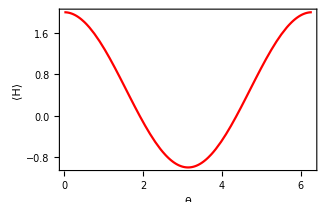

```mathematica
Plot[0.5 + Avgx + Avgy + Avgz,{θ,0,2π},PlotStyle->{Red},FrameLabel-> {"θ","⟨H⟩"}]
```

#### The second example

Now we discuss the second example. The decomposition for the matrix from the sample task in the site

(0 | 0 | 0 | 0
0 | -1 | 1 | 0
0 | 1 | -1 | 0
0 | 0 | 0 | 0)

is:

```mathematica
H2=({{0, 0, 0, 0}, {0, -1, 1, 0}, {0, 1, -1, 0}, {0, 0, 0, 0}});
Decomposition=Solve[H2 == PauliDecomposition,PauliCoefficients]
```

{{c[1]→-1/2,c[2]→0,c[3]→0,c[4]→0,c[5]→0,c[6]→1/2,c[7]→0,c[8]→0,c[9]→0,c[10]→0,c[11]→1/2,c[12]→0,c[13]→0,c[14]→0,c[15]→0,c[16]→1/2}}

Thus, we can write this matrix as:

```mathematica
H2:=1/2(- σ0 ⊗ σ0+σz ⊗ σz +  σx ⊗ σx + σy⊗ σy) ;
```

The eigenstuff for this Matrix is:

```mathematica
Eigenvalues[H2]
Normalize[Eigenvectors[H2]⟦1⟧]//MatrixForm
```

{-2,0,0,0}

(0
-1/(√2)
1/(√2)
0)

The ansatz we can use is : (IX) CX (RZ I) (HI) | 00 >, where angle in RZ is our variational parameter.

```mathematica
CX = ({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 0, 1}, {0, 0, 1, 0}});HG=1/(√2)({{1, 1}, {1, -1}});RZ[θ_]:=({{Exp[-ⅈ θ/2], 0}, {0, Exp[ⅈ θ/2]}})
ClearAll[U,θ]
U[θ_]:=(σ0 ⊗σx).CX.(RZ[θ]⊗σ0).(HG ⊗σ0);
```

The final state vector will be:

```mathematica
U[θ].({1,0}⊗{1,0})//MatrixForm
```

(0
ⅇ^(-(ⅈ θ)/2)/(√2)
ⅇ^((ⅈ θ)/2)/(√2)
0)

We can verify that we simply have to pick θ = π:

```mathematica
-ⅈ U[π].({1,0}⊗{1,0})//MatrixForm
```

(0
-1/(√2)
1/(√2)
0)

Here we show the intermediate steps, with the wave function after the first gate:

```mathematica
(HG ⊗σ0).({1,0}⊗{1,0})//MatrixForm
```

(1/(√2)
0
1/(√2)
0)

The second gate:

```mathematica
(RZ[θ]⊗σ0).(HG ⊗σ0).({1,0}⊗{1,0})//MatrixForm
```

(ⅇ^(-(ⅈ θ)/2)/(√2)
0
ⅇ^((ⅈ θ)/2)/(√2)
0)

The third gate:

```mathematica
CX.(RZ[θ]⊗σ0).(HG ⊗σ0).({1,0}⊗{1,0})//MatrixForm
```

(ⅇ^(-(ⅈ θ)/2)/(√2)
0
0
ⅇ^((ⅈ θ)/2)/(√2))

#### Third Example

Finally, I apply this to one last example

```mathematica
H3 = σz ⊗ σz +  σx ⊗ σy;
H3//MatrixForm
Eigenvalues[H3]
Eigenvectors[H3]⟦1⟧// Normalize//MatrixForm
```

(1 | 0 | 0 | -ⅈ
0 | -1 | ⅈ | 0
0 | -ⅈ | -1 | 0
ⅈ | 0 | 0 | 1)

{-2,2,0,0}

(0
-ⅈ/(√2)
1/(√2)
0)

We can simply apply a (RZ[-π/2]⊗ I) gate after the first Haddamard Gate.

Plotting this:

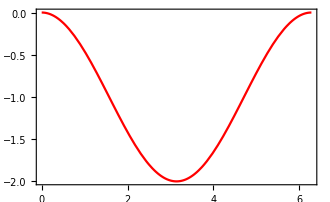

```mathematica
U[θ_]:=(σ0 ⊗σx).CX.(RZ[θ]⊗σ0).(RZ[-π/2]⊗σ0).(HG ⊗σ0);
Subscript[⟨O_⟩, ρψ_]:=If[MatrixQ[ρψ]==True,Tr[ρψ.O],Conjugate[ρψ].O.ρψ]
Avgzz=Subscript[⟨σz⊗ σz⟩, U[θ].({1,0}⊗{1,0})];
Avgxy=Subscript[⟨σx⊗ σy⟩, U[θ].({1,0}⊗{1,0})];
Plot[Avgzz + Avgxy,{θ,0,2π},PlotStyle->{Red}]
```

The final wave function is:

```mathematica
U[θ].({1,0}⊗{1,0})//MatrixForm
```

(0
ⅇ^((ⅈ π)/4-(ⅈ θ)/2)/(√2)
ⅇ^(-(ⅈ π)/4+(ⅈ θ)/2)/(√2)
0)

we can take θ = π to get the correct eigenvalue :

```mathematica
Exp[-I π/4]  U[π].({1,0}⊗{1,0})//MatrixForm
```

(0
-ⅈ/(√2)
1/(√2)
0)